```mathematica
Clear[Lx,Ly,A]
```

```mathematica
Lx=16;
Ly=16;
midPtX = Floor[Lx/2];
midPtY = Floor[Ly/2];
A=Lx*Ly;
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[SitesWithMagFieldInside,Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

512

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
SitesWithMagFieldInside = {{midPtX,midPtY},{midPtX+1,midPtY},{midPtX+1,midPtY+1},{midPtX,midPtY+1},{midPtX,midPtY}};
```

```mathematica
SitesSummedOver ={{midPtX-1,1},{midPtX+2,1},{midPtX+2,Ly},{midPtX-1,Ly},{midPtX-1,1}};
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/(1+Sqrt[5]))*(x-1)+5
LineDn[x_]:=(2/(1+Sqrt[5]))*(x-2)+3
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[ListPts]
ListPts={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[ListPts=Append[ListPts,{x,y}],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

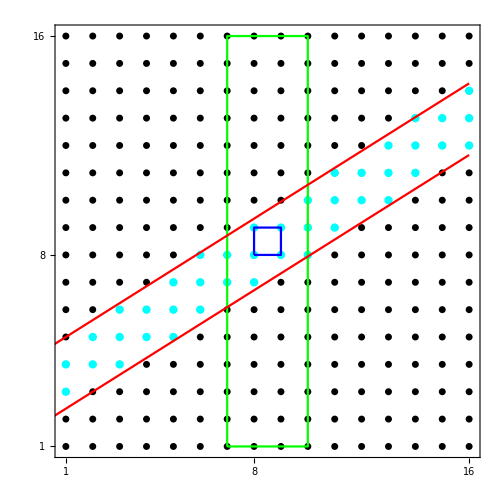

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[ListPts,PlotStyle-> {Cyan,PointSize[0.012]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[SitesWithMagFieldInside,PlotStyle-> {Blue,PointSize[0.01]},Joined-> True],
ListPlot[SitesSummedOver,PlotStyle-> {Green,PointSize[0.01]},Joined-> True],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{17,16},{17,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{18,16},{18,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{19,16},{19,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{20,16},{20,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{21,16},{21,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{22,16},{22,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{23,16},{23,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{24,16},{24,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{25,16},{25,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{26,16},{26,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{27,16},{27,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{28,16},{28,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{29,16},{29,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{30,16},{30,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{31,16},{31,17}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{32,16},{32,17}},2,1]}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None},{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

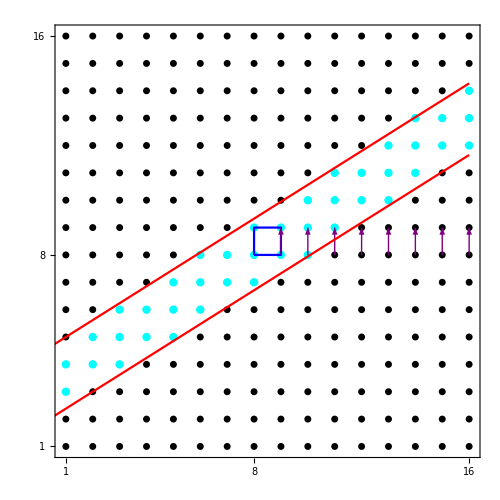

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[ListPts,PlotStyle-> {Cyan,PointSize[0.012]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[SitesWithMagFieldInside,PlotStyle-> {Blue,PointSize[0.01]},Joined-> True],
(** ListPlot[SitesSummedOver,PlotStyle-> {Green,PointSize[0.01]},Joined-> True], **)
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{9,8},{9,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{10,8},{10,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{11,8},{11,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{12,8},{12,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{13,8},{13,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{14,8},{14,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{15,8},{15,9}},2,1]}],
Graphics[{Purple,Arrowheads[{{0.015,0.8}}],Arrow/@Partition[{{16,8},{16,9}},2,1]}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None},{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```